```mathematica
Clear["Global`*"]

dCore=8.2;
NA=0.14;
λ=1.55;
nMat=1.45;
neff=nMat;
β0=2Pi neff/λ;

CalcWindow=20;(*mkm*)
N0=127;
h=5;
```

```mathematica
R=4;
```

```mathematica
StartBeam = Table[HeavisideTheta[x^2+y^2-R^2],{x,-CalcWindow,CalcWindow,2CalcWindow/(N0-1)},{y,-CalcWindow,CalcWindow,2 CalcWindow/(N0-1)}];
```

```mathematica
ArrayPlot[Beam];
```

```mathematica
n=Table[nMat+HeavisideTheta[x^2+y^2-(dCore/2)^2]*(Sqrt[NA^2+nMat^2]-nMat)+0.001I HeavisideTheta[-(x^2+y^2-(10)^2)],{x,-CalcWindow,CalcWindow,2 CalcWindow/(N0-1)},{y,-CalcWindow,CalcWindow,2 CalcWindow/(N0-1)}];
```

```mathematica
Kx=N[ConstantArray[Table[(π k/CalcWindow)^2,{k,0,(N0-1)/2}]~Join~Table[(π (k)/CalcWindow)^2,{k,-Ceiling[N0/2]+1,-1}],N0]];
Dimensions[Kx];
ArrayPlot[Kx];
ListPlot[Kx[[1]]];
```

```mathematica
Ky= Table[(π k/CalcWindow)^2,{k,(-N0+1)/2,(N0-1)/2},{i,(-N0+1)/2,(N0-1)/2}];
Ky=N[RotateLeft[Ky,(N0-1)/2]];
```

```mathematica
Dif=Exp[I (Kx+Ky) h / (2 β0)];
Foc=Exp[-I(β0/neff)^2 (n^2-neff^2)/(2 β0)h];
```

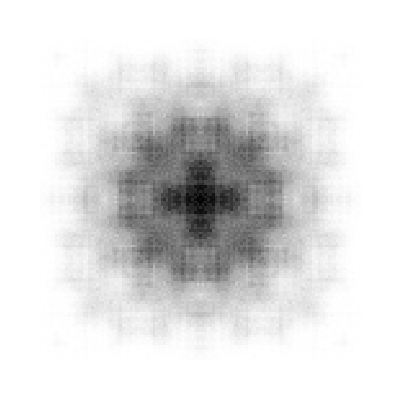

-Graphics-

```mathematica
L=20000;
Beam=StartBeam;
Monitor[
For[ξ=0,ξ<L,ξ+=h,
Beam=InverseFourier[Dif*Fourier[Beam]];
Beam*=Foc;
];
,{ξ}]
ArrayPlot[Abs[Beam]^2]
ListPlot[Abs[Beam[[(N0-1)/2]]]^2]
```